```mathematica
RGBColor256[r_,g_,b_]:=RGBColor[r/255,g/255,b/255];
```

```mathematica
Color1=RGBColor256[255,48,44];
Color2=RGBColor256[255,214,160];
Color3=RGBColor256[172,189,134];
Color4=RGBColor256[40,84,75];
Color5=RGBColor256[1,37,48];
```

```mathematica
PlotColor1=RGBColor256[22,109,178];
PlotColor2=RGBColor256[75,229,17];
PlotColor3=Color1;
```

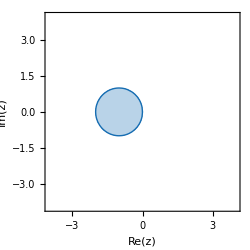

```mathematica
eesr=RegionPlot[Abs[1+(x+y ⅈ)]≤1,{x,-4, 4},{y,-4,4},Axes->True,FrameLabel->{Style["Re(z)",Italic],Style["Im(z)",Italic]},PlotStyle->Lighter[PlotColor1,0.7],BoundaryStyle->Directive[Thick,PlotColor1],ImageSize->250,(*PlotLabel-> Style["Explicit Euler Stability Region",Bold],*)BaseStyle->{FontSize->14,FontFamily->"Sans"}]
```

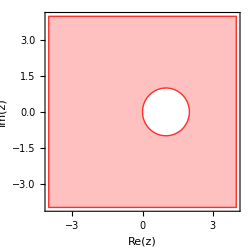

```mathematica
iesr=RegionPlot[Abs[1/(1-(x+y ⅈ))]≤1,{x,-4, 4},{y,-4,4},Axes->True,FrameLabel->{Style["Re(z)",Italic],Style["Im(z)",Italic]},PlotStyle->Lighter[PlotColor3,0.7],BoundaryStyle->Directive[Thick,PlotColor3],ImageSize->250,(*PlotLabel-> Style["Implicit Euler Stability Region",Bold],*)BaseStyle->{FontSize->14,FontFamily->"Sans"}]
```

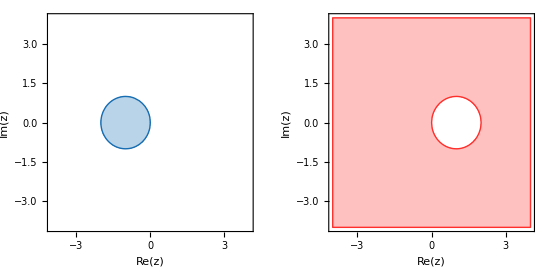

```mathematica
res=Legended[GraphicsRow[{eesr,iesr}],
SwatchLegend[{PlotColor1,PlotColor3},{"Explicit Euler", "Implicit Euler"},LegendLabel->Style["Stability Region of",Bold],LabelStyle->{14,FontFamily->"Sans"},LegendMarkers->"Square"
]
]
```